## Brian — PS 10 — 2025-02-25 — Solution

## EIWL3 Sections 26, 27, and 28

## Exercises from EIWL3 Section 26

```mathematica
(* 26.1 *) Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(* 26.2 *) Blend[{Red,#}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
(* 26.3 *) Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
(* 26.4 *)Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
(* 26.5 *) {EntityValue[#,"Name"],EntityValue[#,"Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]]//Grid[#,Frame->All]&
```

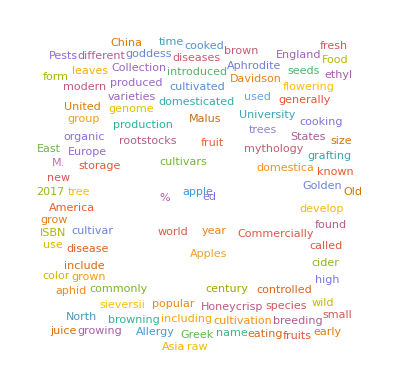
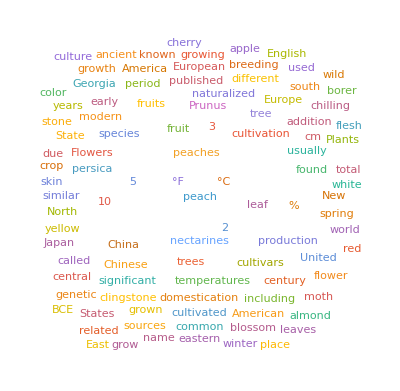
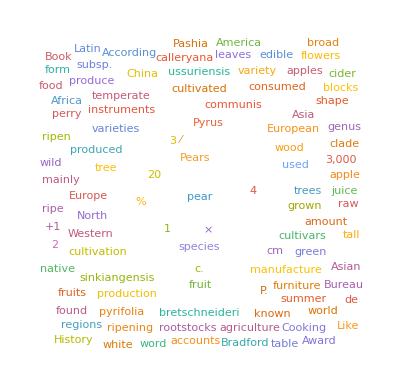

```mathematica
(* 26.6 *) WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

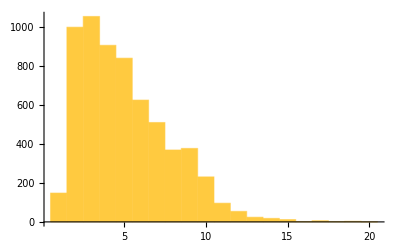
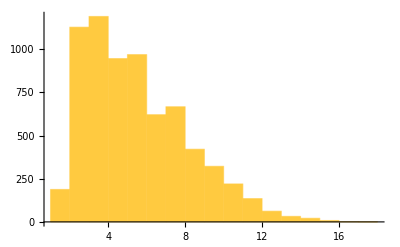
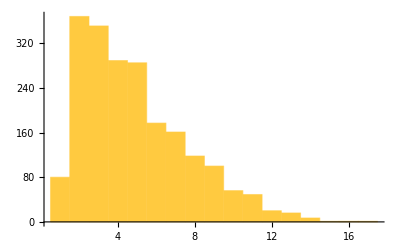

```mathematica
(* 26.7 *) Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

```mathematica
(* 26.8 *)GeoListPlot[#,GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[ EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Exercises from EIWL3 Section 27

```mathematica
(* 27.1 *) NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 27.2 *) NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
(* 27.3 *) NestList[
Rotate[Framed[#],RandomReal[]360°]&,
Style["A",50],
5
]
(* This was another one that I used indentation to help me *)
(* see the organization of the functions and their arguments. *)
```

{A,A,A,A,A,A}

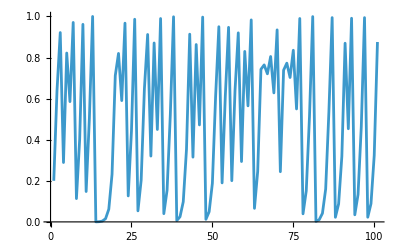

```mathematica
(* 27.4 *) ListLinePlot[NestList[ 4#(1-#)&,0.2,100]]
```

```mathematica
(* 27.5 *) Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
(* 27.6 *) NestList[3#&,1,10] (* This gives 11 results, of course. *)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
(* 27.7 *) NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

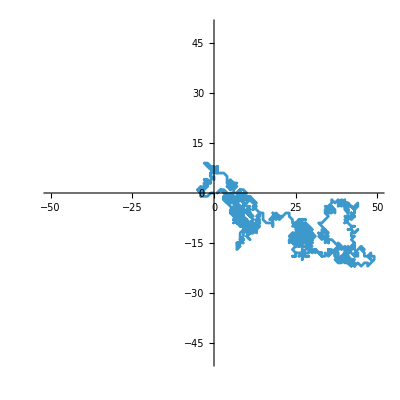

```mathematica
(* 27.8 *) (* Hmmm. He asked for a Graphics. Is it ok that I used a ListLinePlot? *)
(* I used AspectRatio->1 and PlotRange->{{-50,50},{-50,50}} so that the result *)(* wouldn't be scrunched along whichever axis happened the walk went further. *)
ListLinePlot[NestList[#+{RandomChoice[{+1,0,-1}],RandomChoice[{+1,0,-1}]}&,{0,0},1000],AspectRatio->1,PlotRange->{{-50,50},{-50,50}}]
```

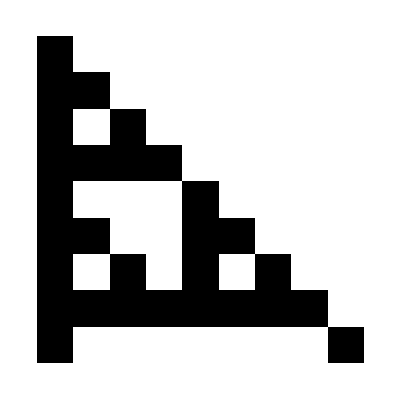

```mathematica
(* 27.9 *) NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},8]//ArrayPlot
```

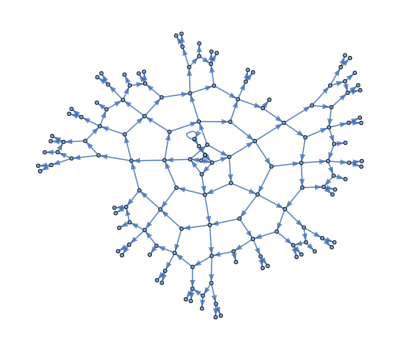

```mathematica
(* 27.10 *) NestGraph[{#+1,2#}&,0,10]
```

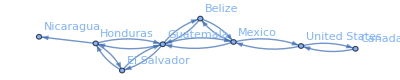

```mathematica
(* 27.11 *) NestGraph[#["BorderingCountries"]&,,4,VertexLabels->All]
```

## Exercises from EIWL3 Section 28

```mathematica
(* 28.1 *) 123^321>456^123
```

True

```mathematica
Total[IntegerDigits[#]]<5&/@3
```

```mathematica
Select[IntegerDigits[#]=={1,2},Range[100]]
```

True

```mathematica
(* 28.2 *) Select[
Range[100],
Total[IntegerDigits[#]]<5&
]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

```mathematica
(* 28.3 *) If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
(* 28.4 *) Select[
WordList[]],

]
```

```mathematica
(* 28.5 *)
```

```mathematica
(* 28.6 *)
```

```mathematica
(* 28.7 *)
```

```mathematica
(* 28.8 *)
```

```mathematica
(* 28.9 *)
```

```mathematica
(* 28.10 *)
```

```mathematica
(* 28.11 *)
```

```mathematica
(* 28.12 *)
```

```mathematica
(* 28.13 *)
```